## Haagerup chain data analysis

### I/O

```mathematica
Labels[type_] := SortBy[StringDrop[StringSplit[#,"/"][[-1]],Switch[type,"m",-2,_,-3]]&/@FileNames[NotebookDirectory[]<>"/"<>type<>"/*."<>type],{Cutoff[#],U[#],J[#],NSites[#]}&];
Job[label_] := StringSplit[label,"_"][[1]];
BC[label_] := StringSplit[label,"_"][[2]];
NSites[label_] := ToExpression[StringSplit[label,"_"][[3]]];
MaxDim[label_] := ToExpression[StringSplit[label,"_"][[4]]];
Cutoff[label_] := StringSplit[label,"_"][[5]];
Prec[label_] := StringSplit[label,"_"][[6]];
J[label_] := StringSplit[label,"_"][[7]];
U[label_] := ToExpression[StringSplit[label,"_"][[8]]];
Charge[label_] := ToExpression[StringSplit[label,"_"][[9]]];
ReadData[label_,type_] := Module[{stream, str},
stream = OpenRead[NotebookDirectory[]<>"/"<>type<>"/"<>label<>"."<>type];
str = ReadString[stream];
Close[stream];
str = StringReplace[str,"e"->"*10^"];
If[type!="m"&&type≠"an",
str = "{" <> StringDrop[StringReplace[StringReplace[str,"\n"->""],",}"->"}"],-1]<> "}"//ToExpression
];
str//ToExpression
];
SetOptions[ListPlot,{BaseStyle->{FontSize->13}, PlotMarkers->{None,Tiny}}];
```

### Dynamical exponent

```mathematica
period = 3;
ζ = (3+Sqrt[13])/2;
j = "0,-1,0";
q = 0;
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]=="haagerupq"&&J[#]==j&&Charge[#]===0&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gaps = {Log[#[[1]]],-Log[#[[2,2,1]]-#[[2,1,1]]]}&/@Select[spectra,Mod[#[[1]],period]==0&][[1;;9]];
ansatz = z L+c;
fit = FindFit[{#[[1]],#[[2]]}&/@gaps,ansatz,{z,c},L];
z0 = SetAccuracy[z/.fit,3];
c0 = SetAccuracy[c/.fit,3];
```

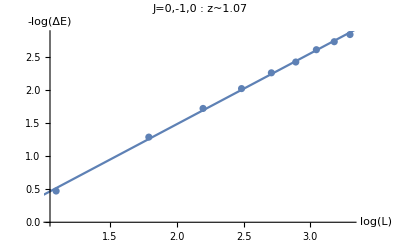

```mathematica
plot = Show[
ListPlot[gaps,AxesLabel->{"log(L)","-log(ΔE)"},
(*PlotLabel->"J=0,-1,0\nlog(ΔE) = -"<>ToString[z0]<>" log(L)+"<>ToString[c0]],*)
PlotLabel->"J=0,-1,0  :  z~"<>ToString[z0]],
Plot[ansatz/.fit,{L,0,4}]
]
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/puredyn.pdf",plot]
```

/Users/yinhslin/Downloads/haagerup-chain/haagerup/puredyn.pdf

### Central charge from entanglement entropy

```mathematica
AnalyzeEE[name_] := Module[{len,Y,X,L,ansatz,fit,model,c,A,x},
Y = ReadData[name,"ee"] ;
len = Length[Y];
X = Y[[-1]];
L = NSites[name];
X = Select[X, L/5<#[[1]]<L*4/5&&OddQ[#[[1]]]&];
ansatz = c/If[BC[name]=="o",6,3] Log[L/π Sin[π x/L]]+A;
fit = FindFit[X,ansatz,{c,A},x];
model = ansatz/.fit;Show[ListPlot[#&/@Y,AxesLabel->{"l","S_l"},PlotLabel->"c = " <> ToString[SetPrecision[c/.fit,3]]<>"  :  J = " <> ToString[J[name]] <> "  L = " <> ToString[NSites[name]],PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])],
Plot[{model},{x,0,L}]]
];
```

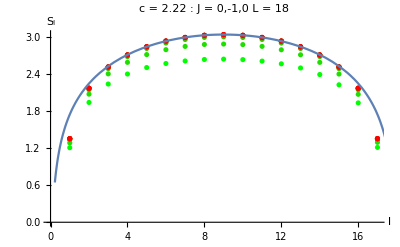

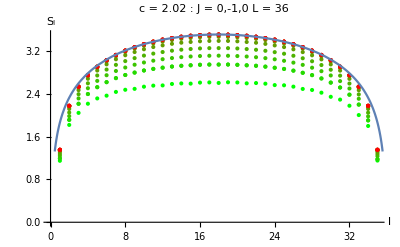

```mathematica
period = 3;
j = "0,-1,0";
plots = AnalyzeEE[#]&/@Select[Labels["ee"],Job[#]== "haagerupq"&&BC[#]=="p"&&Cutoff[#]=="1e-08"&&J[#]==j&&U[#]==2&&Charge[#]==0&&IntegerQ[NSites[#]/period]&&IntegerQ[NSites[#]/18]&];
Print[#]&/@plots;
```

### Scaling dimension from energy

```mathematica
ansatz = α L+β+γ/L+δ/L^2;
fitGSEnergy[gsEnergies_,show_] := Module[{fit,GSEnergy,Energy},
fit = FindFit[{#[[1]],#[[2]]}&/@gsEnergies,ansatz/L,{α,β,γ,δ},L];
If[show,
Print[Show[
ListPlot[gsEnergies,Joined->False,
PlotLabel->ToString[InputForm[ansatz]]<>"\n{α,β,γ,δ} = "<>ToString[SetAccuracy[{α,β,γ,δ}/.fit,4]],
AxesLabel->{"L","E_1"},PlotRange->{{0,36.5},{-.9,Automatic}}],
Plot[ansatz/L/.fit,{L,0,36}]
]];
plot = Show[
ListPlot[gsEnergies,Joined->False,
PlotLabel->"J="<>j,
AxesLabel->{"L","E_1/L"},PlotRange->{{0,36.5},{-.9,Automatic}}],
Plot[ansatz/L/.fit,{L,0,36}]
];
Print[plot];
];
GSEnergy[L0_] := ansatz/.fit/.{L->L0};
Energy[L0_,E0_] := (E0-GSEnergy[L0])/(-γ/.fit)*L0/12;
Energy
];

EnergyPlot[Energy_,spectra_] := ListPlot[Table[Energy[s[[1]],#[[1]]]&/@s[[2]],{s,spectra}],PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[Length[spectra]-1,1]),{k,1,Length[spectra]}])]
```

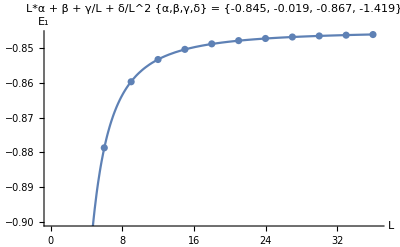

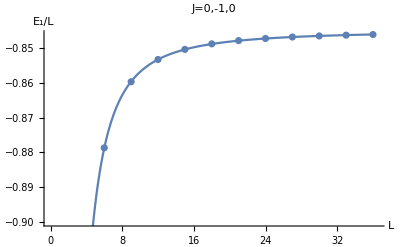

```mathematica
period = 3;
ζ = (3+Sqrt[13])/2;
j = "0,-1,0";
q = 0;
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]=="haagerupq"&&J[#]==j&&Charge[#]===0&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gsEnergies = {#[[1]],#[[2,1,1]]/#[[1]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]=="haagerupq"&&J[#]==j&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy = fitGSEnergy[gsEnergies,True];
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/energy.pdf",plot]
```

/Users/yinhslin/Downloads/haagerup-chain/haagerup/energy.pdf

### Spectral analysis

```mathematica
tol = 5*10^-2;
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[3]]-r]/Abs[r]<tol&],{r,{ζ,-1/ζ}}],
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==2||Abs[#[[3]]-ζ]/ζ>tol&&Abs[#[[3]]+1/ζ]*ζ>tol&]}
]
];

styles = {Black,Black,Red};
markers = {"●","○","●"};
(*styles = {Black,Black,Black};
markers = {"●","○","○"};*)
height = 2.5;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots},
plots = Table[ListPlot[{#[[1]],#[[2]]*c}&/@spectrumByRho[[i]],PlotMarkers->{markers[[i]],9},PlotStyle->styles[[i]]],{i,1,3}];
If[Mod[L,period]==0,
AppendTo[plots, Plot[{1,2},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
If[Mod[L,period]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin}}]],{i,-Floor[L/2],L/2}];
Show[plots,PlotLabel->plotLabel,AxesOrigin->{0,0},PlotRange->{{-L/2,L/2},{0,height}},AxesLabel->{"p","Δ"},ImageSize->{Automatic,200},AspectRatio->height/L]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]=="haagerupq"&&J[#]==j&&Charge[#]===0&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gsEnergies = {#[[1]],#[[2,1,1]]/#[[1]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]=="haagerupq"&&J[#]==j&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy = fitGSEnergy[gsEnergies,False];
Spectrum[Energy,Spec[L0],2,"J="<>j<>"  L="<>ToString[L0]<>"  Q_os="<>ToString[q]]
]
```

```mathematica
Select[Spec[6][[2]],Abs[#[[2]]]<10^-1&&#[[3]]>1&]
```

{{-5.27198,0.,3.30273},{-3.29107,-9.×10^-6,3.30277},{-2.05704,0.000017,3.30251},{-1.99424,0.000025,3.30243},{-1.98883,-8.×10^-6,3.30244}}

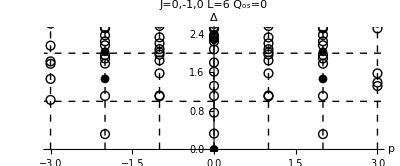

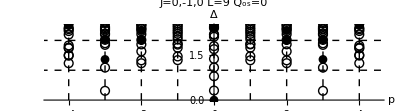

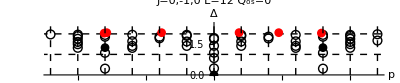

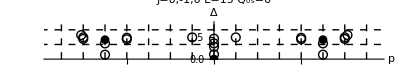

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,6,15,3},{j,{"0,-1,0"}},{q,0,0}]//Flatten;
Print[#]&/@plots;
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec6.pdf",plots[[1]]]
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec9.pdf",plots[[2]]]
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec12.pdf",plots[[3]]]
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec15.pdf",plots[[4]]]
```

/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec6.pdf

/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec9.pdf

/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec12.pdf

/Users/yinhslin/Downloads/haagerup-chain/haagerup/spec15.pdf

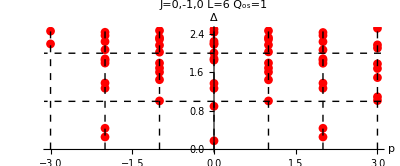

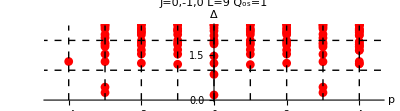

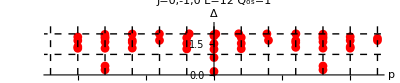

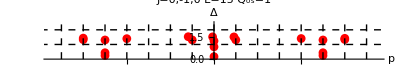

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,6,15,3},{j,{"0,-1,0"}},{q,1,1}]//Flatten;
Print[#]&/@plots;
```

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq6.pdf",plots[[1]]]
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq9.pdf",plots[[2]]]
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq12.pdf",plots[[3]]]
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq15.pdf",plots[[4]]]
```

/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq6.pdf

/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq9.pdf

/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq12.pdf

/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq15.pdf

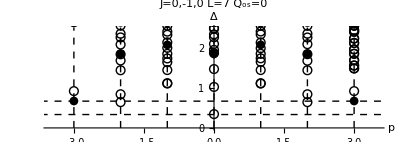

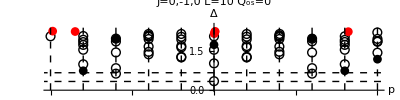

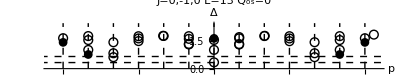

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,7,13,3},{j,{"0,-1,0"}},{q,0,0}]//Flatten;
Print[#]&/@plots;
```

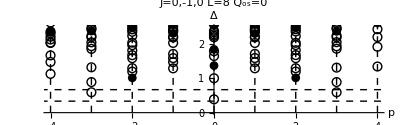

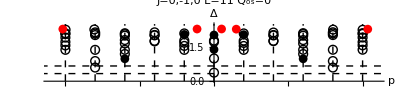

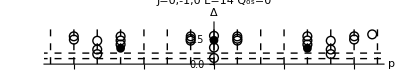

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,8,14,3},{j,{"0,-1,0"}},{q,0,0}]//Flatten;
Print[#]&/@plots;
```

### Partition Function

```mathematica
period = 3;
j = "0,-1,0";
spinPrecision = 10^-2;
c0 = 2;
QLS[L0_,p_] := Round[p/(L0/period)];
Spin[L0_,p_] :=p- QLS[L0,p]*L0/period;
```

```mathematica
PartitionFunction[L0_,j_,c_,DeltaMax_] := Module[{len,Es,partitionFunction,maxE},
SpectrumIncludingFit[L0,j,0];
Es = c*Energy[L0,#[[1]]]&/@Select[Spec[L0][[2]],Abs[Mod[#[[2]],1]]<spinPrecision&]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction = Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]],{i,1,len}];
maxE = Max[Es];

SpectrumIncludingFit[L0,j,1];
Es = c*Energy[L0,#[[1]]]&/@Select[Spec[L0][[2]],Abs[Mod[#[[2]],1]]<spinPrecision&]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction += 2Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]],{i,1,len}];
maxE = Min[maxE,Max[Es]];

partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
partitionFunction = partitionFunction/.{tb->Conjugate[t]}/.t->ⅈ Exp[x];
If[maxE+c/12>DeltaMax,Log[partitionFunction],{}]
]
```

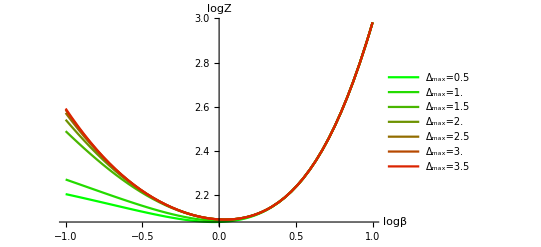

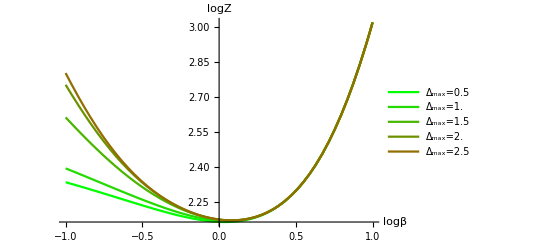

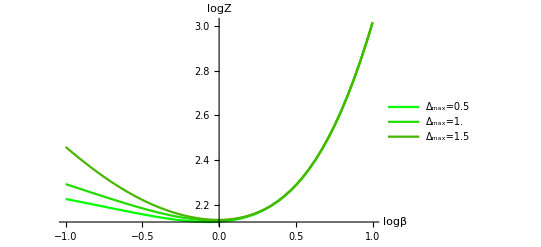

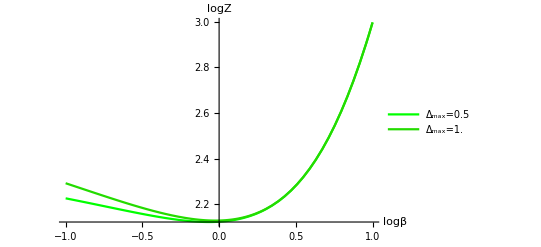

```mathematica
DeltaMaxes = Range[1/2,4,1/2];
Do[
pf = Table[Re[PartitionFunction[L0,j,c0,DeltaMax]],{DeltaMax,DeltaMaxes}];
pf = DeleteCases[pf,{}];
len = Length[DeltaMaxes];
Plot[pf,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}]),AxesLabel->{"logβ","logZ"},PlotLegends->(("Δ_max="<>ToString[N[#]])&/@DeltaMaxes)]//Print
,{L0,6,15,3}]
```

```mathematica
PartitionFunctionZ3[L0_,j_,c_,DeltaMax_] := Module[{len,Es,Rho,partitionFunction,maxE},
SpectrumIncludingFit[L0,j,0];
Es = c*Energy[L0,#[[1]]]&/@Select[Spec[L0][[2]],Abs[Mod[#[[2]],1]]<spinPrecision&]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction = Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]]*Exp[2π ⅈ/3]^QLS[L0,Spec[L0][[2,i,2]]],{i,1,len}];
maxE = Max[Es];

SpectrumIncludingFit[L0,j,1];
Es = c*Energy[L0,#[[1]]]&/@Select[Spec[L0][[2]],Abs[Mod[#[[2]],1]]<spinPrecision&]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction += 2Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]]*Exp[2π ⅈ/3]^QLS[L0,Spec[L0][[2,i,2]]],{i,1,len}];
maxE = Min[maxE,Max[Es]];

partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
partitionFunction = partitionFunction/.{tb->Conjugate[t]}/.t->ⅈ Exp[x];
If[maxE+c/12>DeltaMax,Log[partitionFunction],{}]
]
```

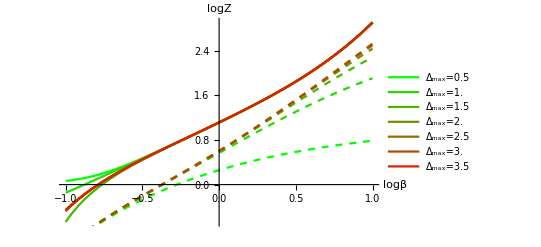

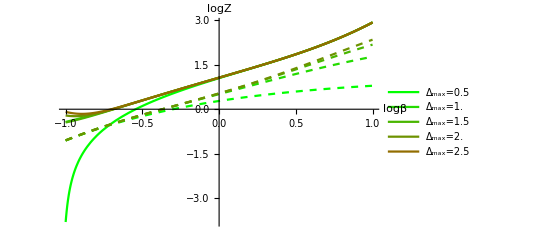

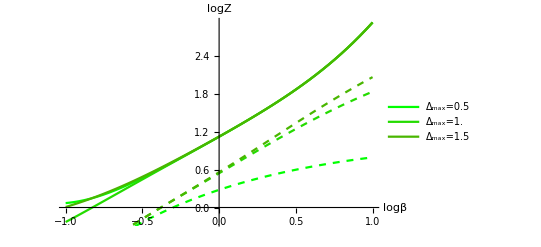

```mathematica
DeltaMaxes = Range[1/2,4,1/2];
Do[
pf1 = Table[Re[PartitionFunctionZ3[L0,j,c0,DeltaMax]],{DeltaMax,DeltaMaxes}];
pf2 = Table[Re[PartitionFunction[L0+1,j,c0,DeltaMax]/.x->-x],{DeltaMax,DeltaMaxes}];
pf1 = DeleteCases[pf1,{}];
pf2 = DeleteCases[pf2,{}];
len = Length[DeltaMaxes];
Show[
Plot[pf1,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}]),AxesLabel->{"logβ","logZ"},PlotLegends->(("Δ_max="<>ToString[N[#]])&/@DeltaMaxes)]
,
Plot[pf2,{x,-1,1},PlotStyle->({Dashed,Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])]
]//Print;
,{L0,6,12,3}]
```

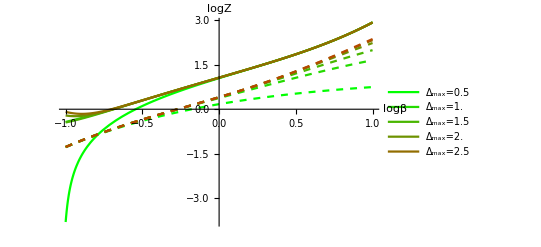

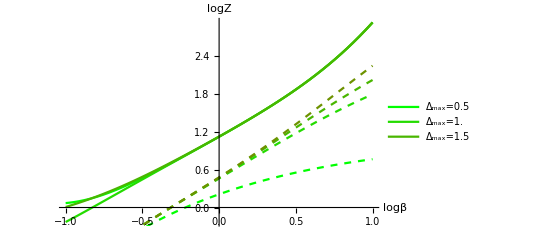

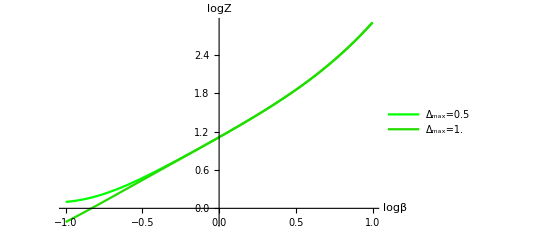

```mathematica
DeltaMaxes = Range[1/2,4,1/2];
Do[
pf1 = Table[Re[PartitionFunctionZ3[L0,j,c0,DeltaMax]],{DeltaMax,DeltaMaxes}];
pf2 = Table[Re[PartitionFunction[L0-1,j,c0,DeltaMax]/.x->-x],{DeltaMax,DeltaMaxes}];
pf1 = DeleteCases[pf1,{}];
pf2 = DeleteCases[pf2,{}];
len = Length[DeltaMaxes];
Show[
Plot[pf1,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}]),AxesLabel->{"logβ","logZ"},PlotLegends->(("Δ_max="<>ToString[N[#]])&/@DeltaMaxes)]
,
Plot[pf2,{x,-1,1},PlotStyle->({Dashed,Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])]
]//Print;
,{L0,9,15,3}]
```

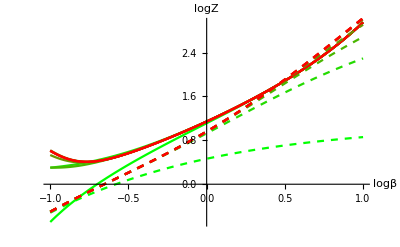

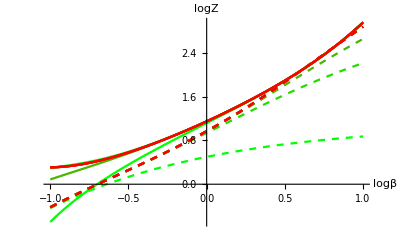

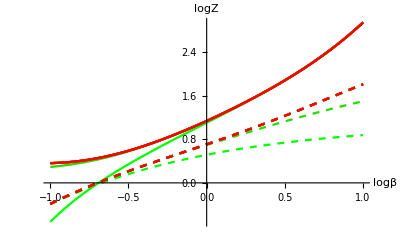

```mathematica
Do[
pf1 = Table[Re[PartitionFunctionZ3[L0,j,c0,DeltaMax]],{DeltaMax,1/2,4,1/2}];
pf2 = Table[Re[PartitionFunction[L0-1,j,c0,DeltaMax]/.x->-x],{DeltaMax,1/2,4,1/2}];
len = Length[pf1];
Show[
Plot[pf1,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}]),AxesLabel->{"logβ","logZ"},PlotLegends->(("Δ_max="<>ToString[N[#]])&/@DeltaMaxes)]
,
Plot[pf2,{x,-1,1},PlotStyle->({Dashed,Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}]),PlotLegends->(("Δ_max="<>ToString[N[#]])&/@DeltaMaxes)]
]//Print;
,{L0,9,15,3}]
```

```mathematica
PartitionFunctionRho[L0_,j_,c_,DeltaMax_] := Module[{len,Es,Rho,partitionFunction},
SpectrumIncludingFit[L0,j,0];
Es = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction = Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]]*Spec[L0][[2,i,3]],{i,1,len}];
partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};

(* Spin of twisted Hilbert space ground state *)
(*Plot[
Re[Log[
(partitionFunction/.{tb->Conjugate[t]}/.{t->ⅈ/β+1})/(partitionFunction/.{tb->Conjugate[t]}/.{t->ⅈ/β})
]/(2π ⅈ)]/.β->Exp[x]
,{x,0,2}]*)

(* Exponential fit *)
(*data = Table[{β,Re[partitionFunction]}/.{tb->Conjugate[t]}/.{t->ⅈ/β},{β,N[1],10,1}];
FindFit[data,a0 Exp[2π β e0]+a1 Exp[2π β(e0+e1)],{a0,e0,a1,e1},β]*)

(*Show[
Plot[Log[partitionFunction/.{tb->Conjugate[t]}/.{t->ⅈ/β}]/(-2π β)/.β->Exp[x],{x,0,2}],
Plot[1/60,{x,0,2},PlotStyle->{Black,Dashed}]
]*)

Log[partitionFunction/.{tb->Conjugate[t]}/.{t->ⅈ/β}]/(-2π β)/.β->Exp[x]
]
```

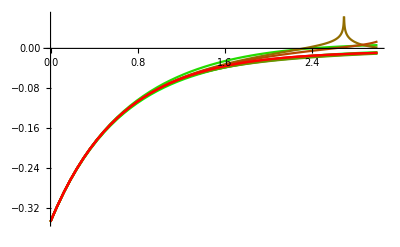

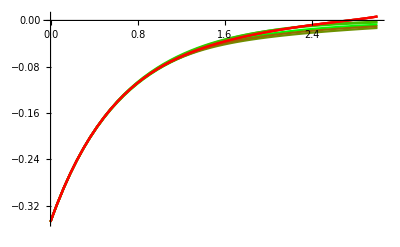

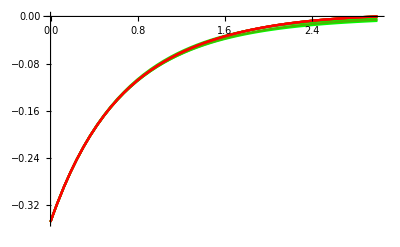

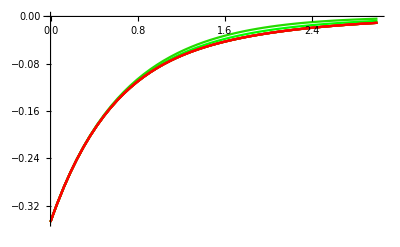

```mathematica
Do[
pf = Table[Re[PartitionFunctionRho[L0,j,c0,DeltaMax]],{DeltaMax,1/2,4,1/2}];
len = Length[pf];
Show[
Plot[pf,{x,0,3},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])]
(*,
Plot[1/60,{x,0,2},PlotStyle->{Black,Dashed}]*)
]//Print
,{L0,6,15,3}]
```

### Modular invariance (old)

```mathematica
ModularInvariance[L0_,j_,c_] := Module[{},
SpectrumIncludingFit[L0,j,0];
E0 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
SpectrumIncludingFit[L0,j,1];
E1 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
partitionFunction = Total[Exp[-2π t*#]&/@E0]+2Total[Exp[-2π t*#]&/@E1];
Plot[partitionFunction/.t->Exp[x],{x,-1,1}]
]
```

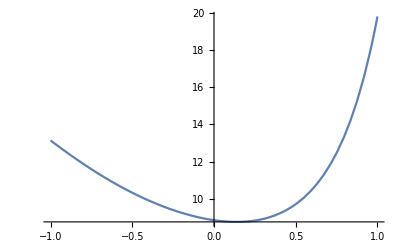

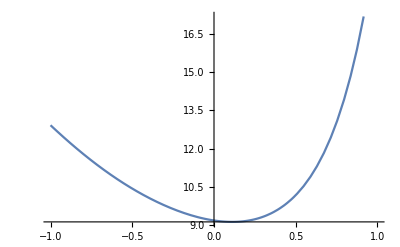

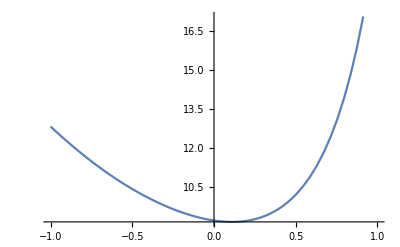

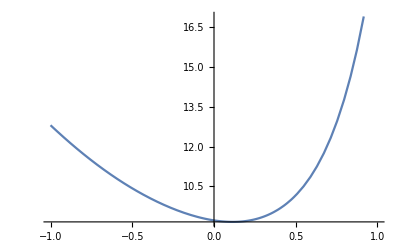

```mathematica
c0 = 2;
ModularInvariance[6,j,c0]
ModularInvariance[9,j,c0]
ModularInvariance[12,j,c0]
ModularInvariance[15,j,c0]
```

```mathematica
ModularInvarianceVar[Ls_,j_,c_,nStates_] := Module[{len,partitionFunctions = {}},
len = Length[Ls];
Do[
SpectrumIncludingFit[L0,j,0];
E0 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
SpectrumIncludingFit[L0,j,1];
E1 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
AppendTo[partitionFunctions,Total[Exp[-2π t*#]&/@E0[[1;;Min[Length[E0],nStates]]]]+2Total[Exp[-2π t*#]&/@E1[[1;;Min[Length[E1],nStates]]]]];
,
{L0,Ls}
];
partitionFunctions = partitionFunctions/.t->Exp[x];
Plot[partitionFunctions,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])]
]
```

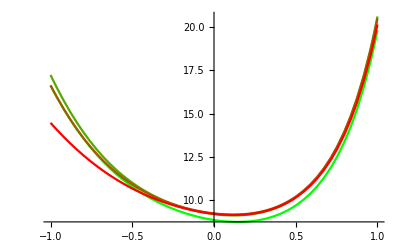

```mathematica
c0 = 2;
ModularInvarianceVar[{6,9,12,15},j,c0,50]
```

```mathematica
ModularInvarianceVar2[L0_,j_,c_,nStates_] := Module[{len,partitionFunctions = {}},
len = Length[nStates];
Do[
SpectrumIncludingFit[L0,j,0];
E0 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
SpectrumIncludingFit[L0,j,1];
E1 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
AppendTo[partitionFunctions,Total[Exp[-2π t*#]&/@E0[[1;;Min[Length[E0],nS]]]]+2Total[Exp[-2π t*#]&/@E1[[1;;Min[Length[E1],nS]]]]];
,
{nS,nStates}
];
partitionFunctions = partitionFunctions/.t->Exp[x];
Plot[partitionFunctions,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])]
]
```

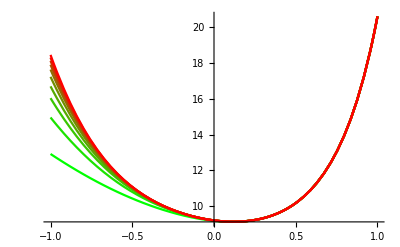

```mathematica
c0 = 2;
ModularInvarianceVar2[9,j,c0,Range[10,100,10]]
```

### Partition Function (old)

```mathematica
PartitionFunction[L0_,j_,c_,len0_] := Module[{len,E0,E1,partitionFunction},
SpectrumIncludingFit[L0,j,0];
len = Min[len0,Length[Spec[L0][[2]]]];
E0 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
partitionFunction = Sum[Exp[-2π ti*E0[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]],{i,1,len}];

SpectrumIncludingFit[L0,j,1];
len = Min[len0,Length[Spec[L0][[2]]]];
E1 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
partitionFunction += 2Sum[Exp[-2π t*E1[[i]]],{i,1,len}];

partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
partitionFunction = partitionFunction/.{tb->-t}/.t->ⅈ Exp[x];
partitionFunction
]
```

```mathematica
Do[
pf = Re[PartitionFunction[L0,j,2]];
Plot[pf,{x,-1,1}]//Print
,{L0,6,15,3}]
```

```mathematica
period = 3;
QLS[L0_,p_] := Round[p/(L0/period)];
Spin[L0_,p_] :=p- QLS[L0,p]*L0/period;
```

```mathematica
PartitionFunctionZ3[L0_,j_,c_] := Module[{len,E0,Rho,partitionFunction},
SpectrumIncludingFit[L0,j,0];
len = Length[Spec[L0][[2]]];
E0 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
partitionFunction = Sum[Exp[-2π ti*E0[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]]*Exp[2π ⅈ/3]^QLS[L0,Spec[L0][[2,i,2]]],{i,1,len}];

SpectrumIncludingFit[L0,j,1];
len = Length[Spec[L0][[2]]];
E1 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
partitionFunction += 2Sum[Exp[-2π ti*E1[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]]*Exp[2π ⅈ/3]^QLS[L0,Spec[L0][[2,i,2]]],{i,1,len}];

partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
partitionFunction = partitionFunction/.{tb->-t}/.t->ⅈ Exp[x];
partitionFunction
]
```

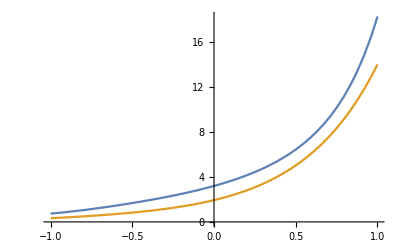

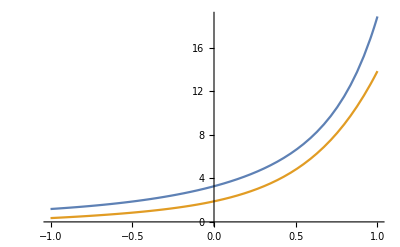

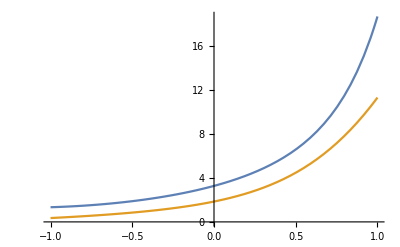

```mathematica
Do[
c0 = 2;
pf1 = Re[PartitionFunctionZ3[L0,j,c0]];
pf2 = Re[PartitionFunction[L0+1,j,c0]/.x->-x];
Plot[{pf1,pf2},{x,-1,1}]//Print;
,{L0,6,12,3}]
```

```mathematica
PartitionFunctionRho[L0_,j_,c_] := Module[{len,E0,Rho,partitionFunction},
SpectrumIncludingFit[L0,j,0];
len = Length[Spec[L0][[2]]];
E0 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
partitionFunction = Sum[Exp[-2π ti*E0[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]],{i,1,len}];
partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
Plot[Log[partitionFunction/.{tb->-t}/.{t->ⅈ/β}]/(-2π β)/.β->Exp[x],{x,0,2}]
(*Plot[Re[partitionFunction]/.{tb->-t}/.t->ⅈ Exp[x],{x,-1,1}]*)
]
```

```mathematica
PartitionFunctionRho[L0_,j_,c_] := Module[{len,E0,Rho,partitionFunction},
SpectrumIncludingFit[L0,j,0];
len = Length[Spec[L0][[2]]];
E0 = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
partitionFunction = Sum[Exp[-2π ti*E0[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]]*Spec[L0][[2,i,3]],{i,1,len}];
partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
Plot[Log[partitionFunction(*/((1+Sqrt[5])/2)*)/.{tb->-t}/.{t->ⅈ/β}]/(-2π β)/.β->Exp[x],{x,0,2}]
(*Plot[Re[partitionFunction]/.{tb->-t}/.t->ⅈ Exp[x],{x,-1,1}]*)
]
```

### Spin-charge relation

```mathematica
SpinCharge2Momentum[k_,L_,s_,q_] := Module[{x = Floor[L/3],y=Mod[L,3],t=3(s-k/9),Q=3q},
(k+Q y)/9+(t+Q x)/3
]
```

```mathematica
Table[SpinCharge2Momentum[0,L,4/3,1],{L,{7,8,10,11,13,14}}]
```

{11/3,4,14/3,5,17/3,6}

```mathematica
Momentum2SpinCharge[k_,L_,p_,tmax_] := Module[{x = Floor[L/3],y=Mod[L,3],t,Q},
{k/9+t/3,Q/9}/.Solve[{p==(k+Q y)/9+(t+Q x)/3,Q∈Integers,t∈Integers,Abs[t]<tmax},{t,Q}]
]
```

```mathematica
Momentum2SpinCharge[0,10,5,8]
```

{{-5/3,2/3},{5/3,1/3}}

## Haagerup chain data analysis - no charge conservation

### Scaling dimension from energy

```mathematica
ansatz = α L+β+γ/L+δ/L^2;
fitGSEnergy[gsEnergies_,show_] := Module[{fit,GSEnergy,Energy},
fit = FindFit[{#[[1]],#[[2]]}&/@gsEnergies,ansatz/L,{α,β,γ,δ},L];
If[show,
Print[Show[
ListPlot[gsEnergies,Joined->False,
PlotLabel->ToString[InputForm[ansatz]]<>"\n{α,β,γ,δ} = "<>ToString[SetAccuracy[{α,β,γ,δ}/.fit,4]],
AxesLabel->{"L","E_1"},PlotRange->{{0,36.5},{-.9,Automatic}}],
Plot[ansatz/L/.fit,{L,0,36}]
]];
plot = Show[
ListPlot[gsEnergies,Joined->False,
PlotLabel->"J="<>j,
AxesLabel->{"L","E_1/L"},PlotRange->{{0,36.5},{-.9,Automatic}}],
Plot[ansatz/L/.fit,{L,0,36}]
];
Print[plot];
];
GSEnergy[L0_] := ansatz/.fit/.{L->L0};
Energy[L0_,E0_] := (E0-GSEnergy[L0])/(-γ/.fit)*L0/12;
Energy
];

EnergyPlot[Energy_,spectra_] := ListPlot[Table[Energy[s[[1]],#[[1]]]&/@s[[2]],{s,spectra}],PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[Length[spectra]-1,1]),{k,1,Length[spectra]}])]
```

```mathematica
period = 3;
ζ = (3+Sqrt[13])/2;
j = "0,-1,0";
q = 0;
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]=="haagerupq"&&J[#]==j&&Charge[#]===0&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gsEnergies = {#[[1]],#[[2,1,1]]/#[[1]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]=="haagerup"&&J[#]==j&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy = fitGSEnergy[gsEnergies,True];
```

-Graphics-

-Graphics-

```mathematica
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/energy.pdf",plot]
```

/Users/yinhslin/Downloads/haagerup-chain/haagerup/energy.pdf

### Spectral analysis

```mathematica
tol = 5*10^-2;
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[3]]-r]/Abs[r]<tol&],{r,{ζ,-1/ζ}}],
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==2||Abs[#[[3]]-ζ]/ζ>tol&&Abs[#[[3]]+1/ζ]*ζ>tol&]}
]
];

styles = {Black,Black,Red};
markers = {"●","○","●"};
(*styles = {Black,Black,Black};
markers = {"●","○","○"};*)
height = 2.5;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots},
plots = Table[ListPlot[{#[[1]],#[[2]]*c}&/@spectrumByRho[[i]],PlotMarkers->{markers[[i]],9},PlotStyle->styles[[i]]],{i,1,3}];
If[Mod[L,period]==0,
AppendTo[plots, Plot[{1,2},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
If[Mod[L,period]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin}}]],{i,-Floor[L/2],L/2}];
Show[plots,PlotLabel->plotLabel,AxesOrigin->{0,0},PlotRange->{{-L/2,L/2},{0,height}},AxesLabel->{"p","Δ"},ImageSize->{Automatic,200},AspectRatio->height/L]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]=="haagerupq"&&J[#]==j&&Charge[#]===0&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gsEnergies = {#[[1]],#[[2,1,1]]/#[[1]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]=="haagerup"&&J[#]==j&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy = fitGSEnergy[gsEnergies,False];
Spectrum[Energy,Spec[L0],2,"J="<>j<>"  L="<>ToString[L0]<>"  Q_os="<>ToString[q]]
]
```

```mathematica
Select[Spec[6][[2]],Abs[#[[2]]]<10^-1&&#[[3]]>1&]
```

{{-5.27198,0.,3.30273},{-3.29107,-9.×10^-6,3.30277},{-2.05704,0.000017,3.30251},{-1.99424,0.000025,3.30243},{-1.98883,-8.×10^-6,3.30244}}

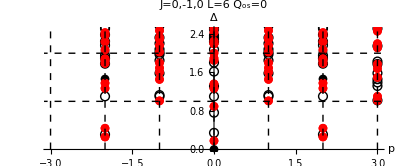

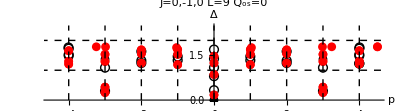

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,6,9,3},{j,{"0,-1,0"}},{q,0,0}]//Flatten;
Print[#]&/@plots;
```

### Partition Function

```mathematica
period = 3;
j = "0,-1,0";
spinPrecision = 10^-2;
c0 = 2;
QLS[L0_,p_] := Round[p/(L0/period)];
Spin[L0_,p_] :=p- QLS[L0,p]*L0/period;
```

```mathematica
PartitionFunction[L0_,j_,c_,DeltaMax_] := Module[{len,Es,partitionFunction,maxE},
SpectrumIncludingFit[L0,j,0];
Es = c*Energy[L0,#[[1]]]&/@Select[Spec[L0][[2]],Abs[Mod[#[[2]],1]]<spinPrecision&]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction = Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]],{i,1,len}];
maxE = Max[Es];

partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
partitionFunction = partitionFunction/.{tb->Conjugate[t]}/.t->ⅈ Exp[x];
If[maxE+c/12>DeltaMax,Log[partitionFunction],{}]
]
```

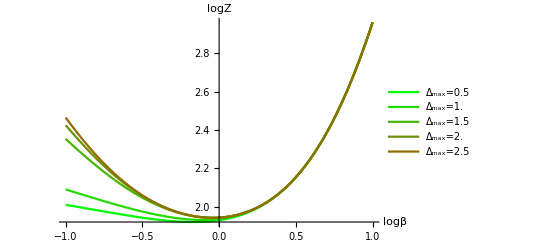

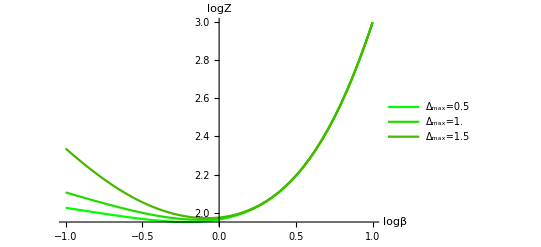

```mathematica
DeltaMaxes = Range[1/2,4,1/2];
Do[
pf = Table[Re[PartitionFunction[L0,j,c0,DeltaMax]],{DeltaMax,DeltaMaxes}];
pf = DeleteCases[pf,{}];
len = Length[DeltaMaxes];
Plot[pf,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}]),AxesLabel->{"logβ","logZ"},PlotLegends->(("Δ_max="<>ToString[N[#]])&/@DeltaMaxes)]//Print
,{L0,6,9,3}]
```

```mathematica
PartitionFunctionZ3[L0_,j_,c_,DeltaMax_] := Module[{len,Es,Rho,partitionFunction,maxE},
SpectrumIncludingFit[L0,j,0];
Es = c*Energy[L0,#[[1]]]&/@Select[Spec[L0][[2]],Abs[Mod[#[[2]],1]]<spinPrecision&]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction = Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]]*Exp[2π ⅈ/3]^QLS[L0,Spec[L0][[2,i,2]]],{i,1,len}];
maxE = Max[Es];

partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
partitionFunction = partitionFunction/.{tb->Conjugate[t]}/.t->ⅈ Exp[x];
If[maxE+c/12>DeltaMax,Log[partitionFunction],{}]
]
```

```mathematica
DeltaMaxes = Range[1/2,4,1/2];
Do[
pf1 = Table[Re[PartitionFunctionZ3[L0,j,c0,DeltaMax]],{DeltaMax,DeltaMaxes}];
pf2 = Table[Re[PartitionFunction[L0+1,j,c0,DeltaMax]/.x->-x],{DeltaMax,DeltaMaxes}];
pf1 = DeleteCases[pf1,{}];
pf2 = DeleteCases[pf2,{}];
len = Length[DeltaMaxes];
Show[
Plot[pf1,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}]),AxesLabel->{"logβ","logZ"},PlotLegends->(("Δ_max="<>ToString[N[#]])&/@DeltaMaxes)]
,
Plot[pf2,{x,-1,1},PlotStyle->({Dashed,Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])]
]//Print;
,{L0,6,9,3}]
```

## golden data analysis

### I/O

```mathematica
Labels[type_] := SortBy[StringDrop[StringSplit[#,"/"][[-1]],Switch[type,"m",-2,_,-3]]&/@FileNames[NotebookDirectory[]<>"/"<>type<>"/*."<>type],{Cutoff[#],U[#],J[#],NSites[#]}&];
Job[label_] := StringSplit[label,"_"][[1]];
BC[label_] := StringSplit[label,"_"][[2]];
NSites[label_] := ToExpression[StringSplit[label,"_"][[3]]];
MaxDim[label_] := ToExpression[StringSplit[label,"_"][[4]]];
Cutoff[label_] := StringSplit[label,"_"][[5]];
Prec[label_] := StringSplit[label,"_"][[6]];
J[label_] := StringSplit[label,"_"][[7]];
U[label_] := ToExpression[StringSplit[label,"_"][[8]]];
Charge[label_] := ToExpression[StringSplit[label,"_"][[9]]];
ReadData[label_,type_] := Module[{stream, str},
stream = OpenRead[NotebookDirectory[]<>"/"<>type<>"/"<>label<>"."<>type];
str = ReadString[stream];
Close[stream];
str = StringReplace[str,"e"->"*10^"];
If[type!="m"&&type≠"an",
str = "{" <> StringDrop[StringReplace[StringReplace[str,"\n"->""],",}"->"}"],-1]<> "}"//ToExpression
];
str//ToExpression
];
SetOptions[ListPlot,{BaseStyle->{FontSize->13}, PlotMarkers->{None,Tiny}}];
```

### Dynamical exponent

```mathematica
period = 2;
ζ = (1+Sqrt[5])/2;
j = "-1";
q = 0;
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],J[#]==j&&Charge[#]===0&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gaps = {Log[#[[1]]],-Log[#[[2,2,1]]-#[[2,1,1]]]}&/@Select[spectra,Mod[#[[1]],period]==0&][[3;;]];
ansatz = z L+c;
fit = FindFit[{#[[1]],#[[2]]}&/@gaps,ansatz,{z,c},L];
z0 = SetAccuracy[z/.fit,3];
c0 = SetAccuracy[c/.fit,3];
```

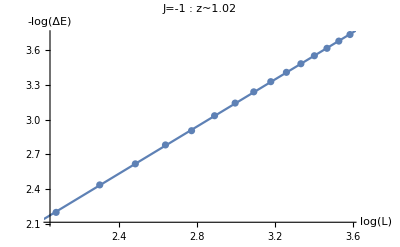

```mathematica
plot = Show[
ListPlot[gaps,AxesLabel->{"log(L)","-log(ΔE)"},
(*PlotLabel->"J=0,-1,0\nlog(ΔE) = -"<>ToString[z0]<>" log(L)+"<>ToString[c0]],*)
PlotLabel->"J=-1  :  z~"<>ToString[z0]],
Plot[ansatz/.fit,{L,0,4}]
]
```

```mathematica
(*Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/puredyn.pdf",plot]*)
```

### Central charge from entanglement entropy

```mathematica
AnalyzeEE[name_] := Module[{len,Y,X,L,ansatz,fit,model,c,A,x},
Y = ReadData[name,"ee"] ;
len = Length[Y];
X = Y[[-1]];
L = NSites[name];
X = Select[X, L/5<#[[1]]<L*4/5&&OddQ[#[[1]]]&];
ansatz = c/If[BC[name]=="o",6,3] Log[L/π Sin[π x/L]]+A;
fit = FindFit[X,ansatz,{c,A},x];
model = ansatz/.fit;Show[ListPlot[#&/@Y,AxesLabel->{"l","S_l"},PlotLabel->"c = " <> ToString[SetPrecision[c/.fit,3]]<>"  :  J = " <> ToString[J[name]] <> "  L = " <> ToString[NSites[name]],PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])],
Plot[{model},{x,0,L}]]
];
```

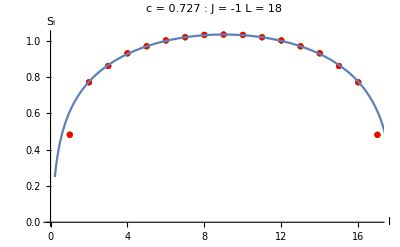

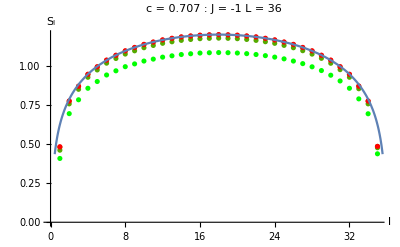

```mathematica
period = 2;
j = "-1";
plots = AnalyzeEE[#]&/@Select[Labels["ee"],Job[#]== "golden"&&BC[#]=="p"&&Cutoff[#]=="1e-08"&&J[#]==j&&U[#]==2&&Charge[#]==0&&IntegerQ[NSites[#]/period]&&IntegerQ[NSites[#]/18]&];
Print[#]&/@plots;
```

### Scaling dimension from energy

```mathematica
ansatz = α L+β+γ/L+δ/L^2;
fitGSEnergy[gsEnergies_,show_] := Module[{fit,GSEnergy,Energy},
fit = FindFit[{#[[1]],#[[2]]}&/@gsEnergies,ansatz/L,{α,β,γ,δ},L];
If[show,
Print[Show[
ListPlot[gsEnergies,Joined->False,
PlotLabel->ToString[InputForm[ansatz]]<>"\n{α,β,γ,δ} = "<>ToString[SetAccuracy[{α,β,γ,δ}/.fit,4]],
AxesLabel->{"L","E_1"},PlotRange->{{0,36.5},{-.78,Automatic}}],
Plot[ansatz/L/.fit,{L,0,36}]
]];
plot = Show[
ListPlot[gsEnergies,Joined->False,
PlotLabel->"J="<>j,
AxesLabel->{"L","E_1/L"},PlotRange->{{0,36.5},{-.78,Automatic}}],
Plot[ansatz/L/.fit,{L,0,36}]
];
Print[plot];
];
GSEnergy[L0_] := ansatz/.fit/.{L->L0};
Energy[L0_,E0_] := (E0-GSEnergy[L0])/(-γ/.fit)*L0/12;
Energy
];

EnergyPlot[Energy_,spectra_] := ListPlot[Table[Energy[s[[1]],#[[1]]]&/@s[[2]],{s,spectra}],PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[Length[spectra]-1,1]),{k,1,Length[spectra]}])]
```

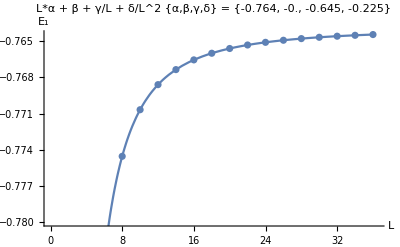

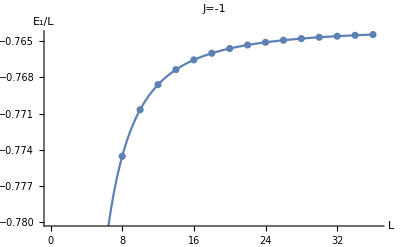

```mathematica
period = 2;
ζ = (1+Sqrt[5])/2;
j = "-1";
q = 0;
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],J[#]==j&&Charge[#]===0&&NSites[#]>6&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gsEnergies = {#[[1]],#[[2,1,1]]/#[[1]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],J[#]==j&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy = fitGSEnergy[gsEnergies,True];
```

```mathematica
(*Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/energy.pdf",plot]*)
```

### Spectral analysis

```mathematica
tol = 1*10^-2;
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[3]]-r]/Abs[r]<tol&],{r,{ζ,-1/ζ}}],
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==2||Abs[#[[3]]-ζ]/ζ>tol&&Abs[#[[3]]+1/ζ]*ζ>tol&]}
]
];

styles = {Black,Black,Red};
markers = {"●","○","●"};
(*styles = {Black,Black,Black};
markers = {"●","○","○"};*)
height = 2.5;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots},
plots = Table[ListPlot[{#[[1]],#[[2]]*c}&/@spectrumByRho[[i]],PlotMarkers->{markers[[i]],9},PlotStyle->styles[[i]]],{i,1,3}];
If[Mod[L,period]==0,
AppendTo[plots, Plot[{1,2},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
If[Mod[L,period]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin}}]],{i,-Floor[L/2],L/2}];
Show[plots,PlotLabel->plotLabel,AxesOrigin->{0,0},PlotRange->{{-L/2,L/2},{0,height}},AxesLabel->{"p","Δ"},ImageSize->{Automatic,200},AspectRatio->height/L]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],J[#]==j&&Charge[#]===0&&NSites[#]>6&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
gsEnergies = {#[[1]],#[[2,1,1]]/#[[1]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],J[#]==j&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy = fitGSEnergy[gsEnergies,False];
Spectrum[Energy,Spec[L0],0.7,"J="<>j<>"  L="<>ToString[L0]<>"  Q_os="<>ToString[q]]
]
```

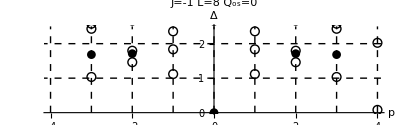

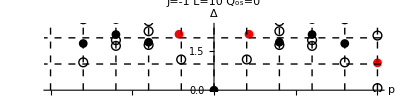

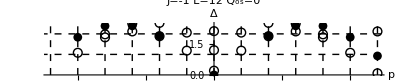

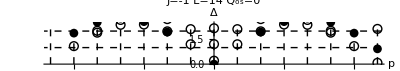

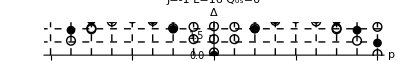

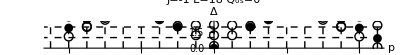

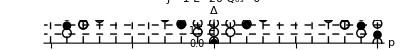

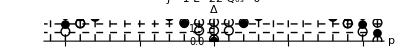

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,8,36,2},{j,{"-1"}},{q,0,0}]//Flatten;
Print[#]&/@plots;
```

```mathematica
(*Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq6.pdf",plots[[1]]]
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq9.pdf",plots[[2]]]
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq12.pdf",plots[[3]]]
Export["/Users/yinhslin/Downloads/haagerup-chain/haagerup/specq15.pdf",plots[[4]]]*)
```

### Partition Function

```mathematica
period = 2;
j = "-1";
QLS[L0_,p_] := Round[p/(L0/period)];
Spin[L0_,p_] :=p- QLS[L0,p]*L0/period;
```

```mathematica
PartitionFunction[L0_,j_,c_,DeltaMax_] := Module[{len,Es,partitionFunction},
SpectrumIncludingFit[L0,j,0];
Es = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction = Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]],{i,1,len}];
partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
partitionFunction = partitionFunction/.{tb->Conjugate[t]}/.t->ⅈ Exp[x];
Log[partitionFunction]
]
```

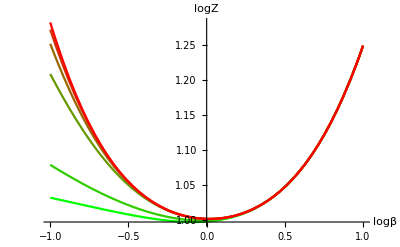

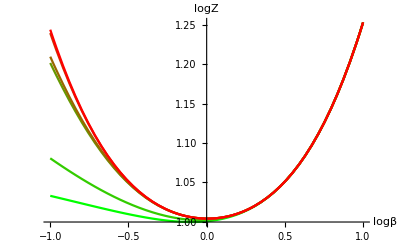

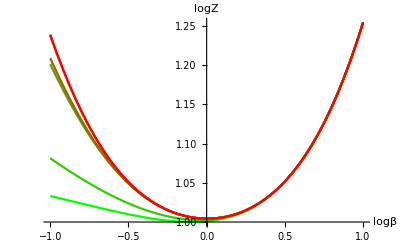

```mathematica
Do[
pf = Table[Re[PartitionFunction[L0,j,.7,DeltaMax]],{DeltaMax,1/2,3,1/2}];
len = Length[pf];
Plot[pf,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}]),AxesLabel->{"logβ","logZ"}]//Print
,{L0,12,36,12}]
```

```mathematica
PartitionFunctionZ2[L0_,j_,c_,DeltaMax_] := Module[{len,Es,Rho,partitionFunction},
SpectrumIncludingFit[L0,j,0];
Es = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction = Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]]*(-1)^QLS[L0,Spec[L0][[2,i,2]]],{i,1,len}];
partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};
partitionFunction = partitionFunction/.{tb->Conjugate[t]}/.t->ⅈ Exp[x];
Log[partitionFunction]
]
```

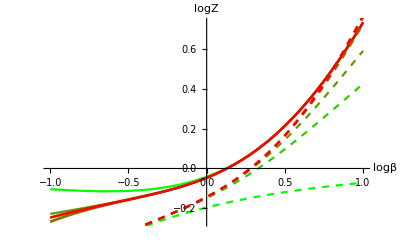

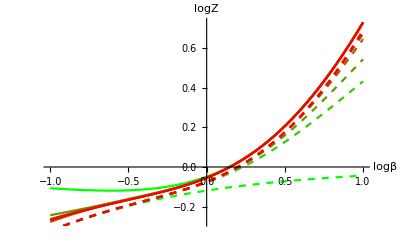

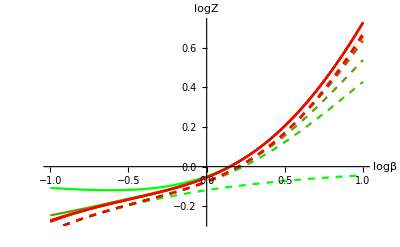

```mathematica
Do[
pf1 = Table[Re[PartitionFunctionZ2[L0,j,.7,DeltaMax]],{DeltaMax,1/2,3,1/2}];
pf2 = Table[Re[PartitionFunction[L0-1,j,.7,DeltaMax]/.x->-x],{DeltaMax,1/2,3,1/2}];
len = Length[pf1];
Show[
Plot[pf1,{x,-1,1},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}]),AxesLabel->{"logβ","logZ"}]
,
Plot[pf2,{x,-1,1},PlotStyle->({Dashed,Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])]
]//Print;
,{L0,12,36,12}]
```

```mathematica
PartitionFunctionRho[L0_,j_,c_,DeltaMax_] := Module[{len,Es,Rho,partitionFunction},
SpectrumIncludingFit[L0,j,0];
Es = c*Energy[L0,#[[1]]]&/@Spec[L0][[2]]-c/12;
len = Length[Select[Es,#<DeltaMax-c/12&]];
partitionFunction = Sum[Exp[-2π ti*Es[[i]]+2π ⅈ tr*Spin[L0,Spec[L0][[2,i,2]]]]*Spec[L0][[2,i,3]],{i,1,len}];
partitionFunction = partitionFunction/.{tr->(t+tb)/2,ti->(t-tb)/(2ⅈ)};

(* Spin of twisted Hilbert space ground state *)
(*Plot[
Re[Log[
(partitionFunction/.{tb->Conjugate[t]}/.{t->ⅈ/β+1})/(partitionFunction/.{tb->Conjugate[t]}/.{t->ⅈ/β})
]/(2π ⅈ)]/.β->Exp[x]
,{x,0,2}]*)

(* Exponential fit *)
(*data = Table[{β,Re[partitionFunction]}/.{tb->Conjugate[t]}/.{t->ⅈ/β},{β,N[1],10,1}];
FindFit[data,a0 Exp[2π β e0]+a1 Exp[2π β(e0+e1)],{a0,e0,a1,e1},β]*)

(*Show[
Plot[Log[partitionFunction/.{tb->Conjugate[t]}/.{t->ⅈ/β}]/(-2π β)/.β->Exp[x],{x,0,2}],
Plot[1/60,{x,0,2},PlotStyle->{Black,Dashed}]
]*)

Log[partitionFunction/.{tb->Conjugate[t]}/.{t->ⅈ/β}]/(-2π β)/.β->Exp[x]
]
```

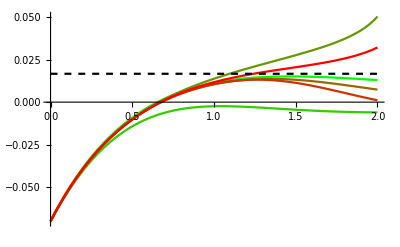

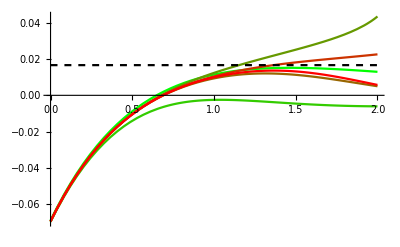

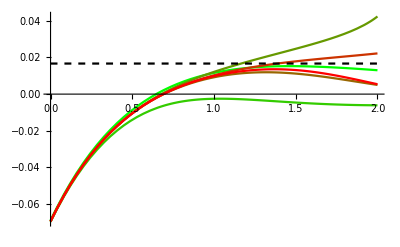

```mathematica
Do[
pf = Table[Re[PartitionFunctionRho[L0,j,.7,DeltaMax]],{DeltaMax,1/2,3,1/2}];
len = Length[pf];
Show[
Plot[pf,{x,0,2},PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])],
Plot[1/60,{x,0,2},PlotStyle->{Black,Dashed}]
]//Print
,{L0,12,36,12}]
```